This mathematica notebook is attached to the paper 2109.xxxxx by Antoine Bourget, Julius Grimminger, Amihay Hanany, Rudolph Kalveks and Zhenghao Zhong. 
Please cite the paper above if you use this code. 

There is only one routine: 

MagneticQuivers[flavorNodes_,gaugeNodes_,usu_,style_]

This takes as an input the list of flavor nodes and gauge nodes, along with the type of each gauge group ("u" for unitary and "s" for special unitary). The output is a list of magnetic quivers, one for each cone of the Higgs branch variety of the initial quiver. The algorithm is described in the paper, and uses the concept of web locking in webs of 5-branes in type IIB superstring theory.   
"style" is a parameter that can be True or False and only influences the aesthetics of the drawings. 

See examples in the section below.

## Code

```mathematica
MagneticQuivers[flavorNodes_,gaugeNodes_,usu_,style_]:=Module[{nf,n,verticalBranes,transpose,cumul,totalBranesLeft,gaugeNodesExt,flavorNodesExt,slopesBranes,collapsePair,collapsePartitionOnce,collapse,braneSrule,leftBranesTableMaxLength,fullTableleft,fullTableright,blackNodes,positiveBlackNodes,quiver,compareLockingsVertical,ppos,colors,pos,allLockings,lockingPatterns,braneLockingsCompatibleUSU,braneLockings,goodBraneLockings,compareLockingsHorizontal,dominantLockings,finalGraph},

nf=Total[flavorNodes];
n=Length[gaugeNodes];
verticalBranes=Range[n+1];
transpose[part_]:=Table[Length[Select[part,#≥i&]],{i,1,Max[part]}];
cumul[part_]:=Table[Sum[part[[j]],{j,i,Length[part]}],{i,1,Length[part]}];
totalBranesLeft=Reverse[cumul[transpose[cumul[flavorNodes]]]];
gaugeNodesExt=Join[{0},gaugeNodes,{0}];
flavorNodesExt=Join[{0},flavorNodes,{0}];slopesBranes=Table[gaugeNodesExt[[i]]-gaugeNodesExt[[i+1]]+Sum[flavorNodesExt[[j]],{j,i+1,n+1}],{i,1,n+1}];


(* Collapsing Algorithm *)
collapsePair[{a_,b_}]:=If[a>b,{a,b},{a+b-Floor[(a+b)/2],Floor[(a+b)/2]}];
collapsePartitionOnce[part_]:=Module[{unordered,index},
unordered=Select[Range[Length[part]-1],part[[#]]<part[[#+1]]&];
If[unordered==={},part,
index=Min[unordered];
Join[Table[part[[i]],{i,1,index-1}],collapsePair[{part[[index]],part[[index+1]]}],Table[part[[i]],{i,index+2,Length[part]}]]
]
];
collapse[part_]:=If[collapsePartitionOnce[part]===part,part,collapse[collapsePartitionOnce[part]]];
braneSrule[group_]:=cumul[transpose[collapse[slopesBranes[[group]]]]];
leftBranesTableMaxLength[braneLocking_]:=Max[Table[Length[braneSrule[group]],{group,braneLocking}]];
fullTableleft[braneLocking_]:=Table[Reverse[PadRight[braneSrule[group],nf]],{group,braneLocking}];fullTableright[braneLocking_]:=Table[Table[Sum[If[j>i,slopesBranes[[j]],0],{j,group}],{i,1,n}],{group,braneLocking}];
blackNodes[braneLocking_]:=totalBranesLeft-Total/@Transpose[fullTableleft[braneLocking]];
positiveBlackNodes[braneLocking_]:=Module[{bn},
bn=blackNodes[braneLocking];
Abs[bn]===bn
];


(* Main procedure *)
quiver[braneLocking_]:=Module[{nc,ftLeft,ftRight,intersectionLeft,intersectionRight,blackNods,indicesBlackNonZero,nb,intersectionMatrixAux,intersectionMatrix,ranksMagneticQuiver,balances,vertexLabels,vertexCoordinates,vertexStyle,vertexSizes,graph},
nc=Length[braneLocking];
ftLeft=fullTableleft[braneLocking];
ftRight=fullTableright[braneLocking];
intersectionLeft[Locking1_,Locking2_]:=Module[{line1,line2},
line1=ftLeft[[Locking1]];
line2=ftLeft[[Locking2]];
Sum[line1[[i]]*line2[[i+1]]+line2[[i]]*line1[[i+1]]-2*line1[[i]]*line2[[i]],{i,1,nf-1}]-line1[[nf]]*line2[[nf]]];
intersectionRight[Locking1_,Locking2_]:=Sum[If[i≤n,ftRight[[Locking2,i]],0],{i,braneLocking[[Locking1]]}]+Sum[If[i≤n,ftRight[[Locking1,i]],0],{i,braneLocking[[Locking2]]}];
blackNods=blackNodes[braneLocking];
indicesBlackNonZero=Select[Range[nf],blackNods[[#]]>0&];
nb=Length[indicesBlackNonZero];
(* The total intersection matrix has first the colors, from 1 to nc, and then the black dots, from nc+1 to nc+nb *)
intersectionMatrixAux=Table[Table[
If[i1≥i2,0,
If[i2≤nc,intersectionLeft[i1,i2]+intersectionRight[i1,i2],
If[i2>nc≥i1,ftLeft[[i1,indicesBlackNonZero[[i2-nc]]+1]]-2ftLeft[[i1,indicesBlackNonZero[[i2-nc]]+0]]+If[(indicesBlackNonZero[[i2-nc]]-1)==0,0,ftLeft[[i1,indicesBlackNonZero[[i2-nc]]-1]]],
If[Abs[i1-i2]==1,1,0]
]]]
,{i2,1,nc+nb}],{i1,1,nc+nb}];
intersectionMatrix=intersectionMatrixAux+Transpose[intersectionMatrixAux];
ranksMagneticQuiver=Join[Table[1,{i,1,nc}],Select[blackNods,Not[#===0]&]];
balances=intersectionMatrix.ranksMagneticQuiver-2ranksMagneticQuiver;
vertexLabels=Table[i->ranksMagneticQuiver[[i]],{i,1,Length[ranksMagneticQuiver]}];
vertexCoordinates=Table[If[i>nc,{i-nf,0},{2(RandomReal[]-.5)+Sum[(j-nf)*intersectionMatrix[[i,j]],{j,nc+1,nc+nb}]/Max[1,Sum[intersectionMatrix[[i,j]],{j,nc+1,nc+nb}]],-1-RandomReal[]}],{i,1,Length[ranksMagneticQuiver]}];
vertexStyle=Table[If[i<nf,If[balances[[i]]==0,i->White,i->Cyan],If[balances[[i]]==0,i->White,i->Cyan]],{i,1,Length[ranksMagneticQuiver]}];
vertexSizes=Table[If[i<nf,i->Normal,i->Normal],{i,1,Length[ranksMagneticQuiver]}];
graph=If[style,AdjacencyGraph[intersectionMatrix,VertexLabels->vertexLabels,VertexStyle->vertexStyle,VertexSize->vertexSizes,VertexCoordinates->vertexCoordinates],AdjacencyGraph[intersectionMatrix,VertexStyle->vertexStyle,VertexSize->vertexSizes,VertexLabels->vertexLabels]];
{graph,MatrixForm[intersectionMatrix],MatrixForm[ranksMagneticQuiver]}
];


(* Select only the lockings which correspond to the chosen USU *)
compareLockingsVertical[set1_,set2_]:=(* Says if set1 is more locked than set2 *)Apply[And,Table[Apply[Or,Table[SubsetQ[s1,s2],{s1,set1}]],{s2,set2}]];
ppos=Position[usu,"s"];
If[ppos=={},
colors={Range[n+1]-1};
,
pos=Transpose[ppos][[1]];
colors=Join[{Table[j,{j,0,pos[[1]]-1}]},Table[Table[j,{j,pos[[i]],pos[[i+1]]-1}],{i,1,Length[pos]-1}],{Table[j,{j,Last[pos],n}]}];
];
allLockings[list_]:=DeleteDuplicates[Sort[If[Length[list]==0,{{}},If[Length[list]==1,{{{list[[1]]}}},
Sort/@Flatten[Table[Table[Join[{Complement[list,s]},c],{c,allLockings[s]}],{s,Subsets[list,Length[list]-1]}],1]]]]];
lockingPatterns=allLockings[Range[Length[colors]]];
braneLockingsCompatibleUSU=Table[Table[1+Flatten[Table[colors[[i]],{i,ccc}]],{ccc,lockingPattern}],{lockingPattern,lockingPatterns}];

(* Generate all good Lockings : S-rule satisfied and no negative number of branes *)
braneLockings=Select[braneLockingsCompatibleUSU,leftBranesTableMaxLength[#]≤nf&];
goodBraneLockings=Select[braneLockings,positiveBlackNodes[#]&];


(* Select only the dominant Lockings *)
compareLockingsHorizontal[set1_,set2_]:=(* Says if set1 gives more Srule freedom than set2 *)Module[{b1,b2},
b1=blackNodes[set1];
b2=blackNodes[set2];
Abs[b1-b2]===b1-b2&&Not[Abs[b1-b2]===0*b1]
];
dominantLockings=Select[goodBraneLockings,Not[Apply[Or,Table[If[#==s2,False,Not[compareLockingsHorizontal[#,s2]]&&compareLockingsVertical[#,s2]],{s2,goodBraneLockings}]]]&];

(* Print the electric quiver *)
Module[{nonzeroindices,radius,disks,rectangles,linesHor,linesVert,textGauge,textFlav},
nonzeroindices=Select[Range[Length[flavorNodes]],flavorNodes[[#]]≠0&];
radius=.15;
disks=Table[Disk[{i,0},radius],{i,1,Length[flavorNodes]}];
rectangles=Table[Rectangle[{i,1}-{radius,radius},{i,1}+{radius,radius}],{i,nonzeroindices}];
linesHor=Table[Line[{{i,0},{i+1,0}}],{i,1,Length[flavorNodes]-1}];
linesVert=Table[Line[{{i,0},{i,1}}],{i,nonzeroindices}];
textFlav=Table[Text[Style[ToString[flavorNodes[[i]]]],{i,1+2radius}],{i,nonzeroindices}];
textGauge=Table[Text[Style[If[usu[[i]]=="s",StringJoin["SU(",ToString[gaugeNodes[[i]]],")"],StringJoin["U(",ToString[gaugeNodes[[i]]],")"]]],{i,-2radius}],{i,1,Length[flavorNodes]}];
finalGraph=Graphics[Join[{Black},disks,rectangles,linesHor,linesVert,textFlav,textGauge],ImageSize->Small];
];
Print["Electric quiver :"];
Print[finalGraph];


(* Print all the quivers *)
Print["List of magnetic quivers :"];Print["---------------------"];
Do[
Print["Brane Locking : ",braneLocking-1];
Print[{{"Quiver","Adjacency Matrix","Ranks U(n)"},quiver[braneLocking]}//TableForm];
Print["---------------------"];
,{braneLocking,dominantLockings}];
];
```

## Examples

### Basic Examples

Electric quiver :

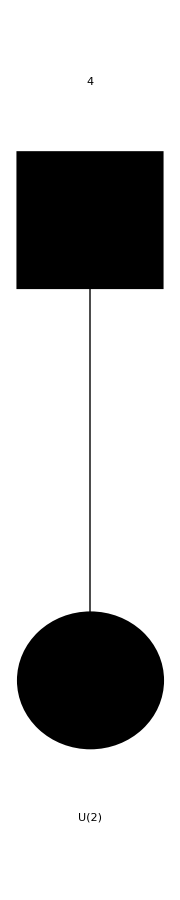

List of magnetic quivers :

---------------------

Brane Locking : {{0,1}}

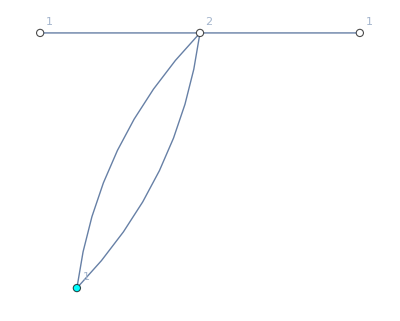
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 2 | 0
0 | 0 | 1 | 0
2 | 1 | 0 | 1
0 | 0 | 1 | 0) | (1
1
2
1)

---------------------

```mathematica
MagneticQuivers[{4},{2},{"u"},True]
```

Electric quiver :

-Graphics-

List of magnetic quivers :

---------------------

Brane Locking : {{0,1}}

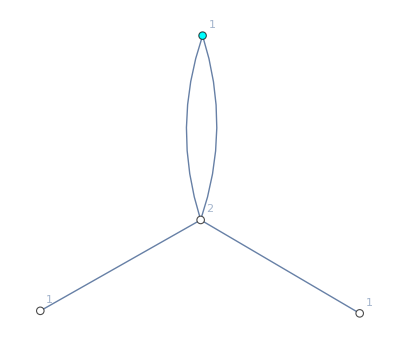
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 2 | 0
0 | 0 | 1 | 0
2 | 1 | 0 | 1
0 | 0 | 1 | 0) | (1
1
2
1)

---------------------

```mathematica
MagneticQuivers[{4},{2},{"u"},False]
```

Electric quiver :

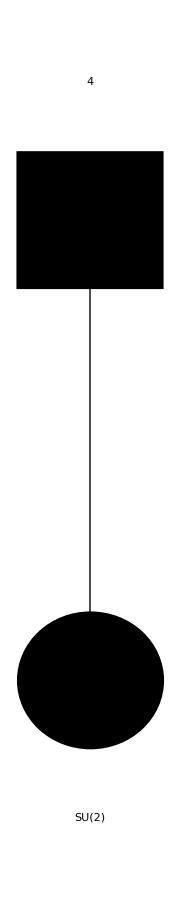

List of magnetic quivers :

---------------------

Brane Locking : {{0},{1}}

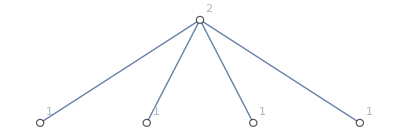
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0) | (1
1
1
2
1)

---------------------

```mathematica
MagneticQuivers[{4},{2},{"s"},False]
```

### Examples from our paper

#### Simple example discussed in Section 4.1

Electric quiver :

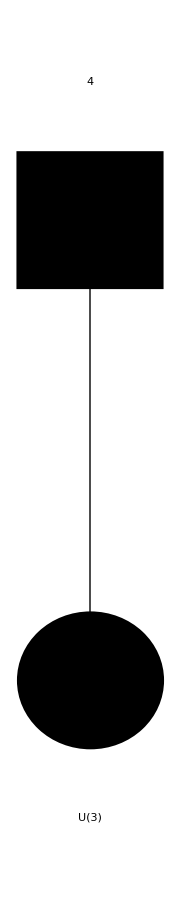

List of magnetic quivers :

---------------------

Brane Locking : {{0,1}}

Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 2 | 0
0 | 0 | 1 | 0
2 | 1 | 0 | 1
0 | 0 | 1 | 0) | (1
1
2
1)

---------------------

```mathematica
MagneticQuivers[{4},{3},{"u"},False]
```

Electric quiver :

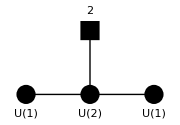

List of magnetic quivers :

---------------------

Brane Locking : {{0,1,2,3}}

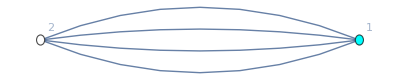
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 4
4 | 0) | (1
2)

---------------------

```mathematica
(* Input magnetic quiver computed above (after ungauging the overbalanced U(1)) *)
MagneticQuivers[{0,2,0},{1,2,1},{"u","u","u"},False]
```

Electric quiver :

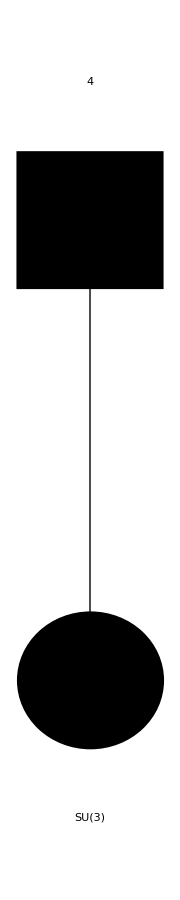

List of magnetic quivers :

---------------------

Brane Locking : {{0,1}}

Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 2 | 0
0 | 0 | 1 | 0
2 | 1 | 0 | 1
0 | 0 | 1 | 0) | (1
1
2
1)

---------------------

Brane Locking : {{0},{1}}

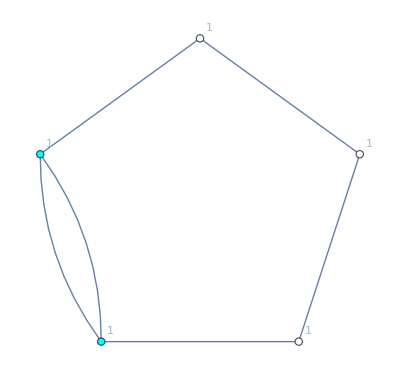
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 2 | 0 | 0 | 1
2 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0) | (1
1
1
1
1)

---------------------

```mathematica
(* Related Example *)
MagneticQuivers[{4},{3},{"s"},False]
```

#### Examples Summarised in Table 2

Electric quiver :

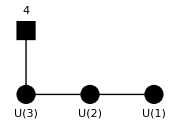

List of magnetic quivers :

---------------------

Brane Locking : {{0,1,2,3}}

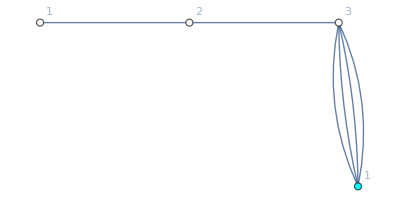
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 0 | 4
0 | 0 | 1 | 0
0 | 1 | 0 | 1
4 | 0 | 1 | 0) | (1
1
2
3)

---------------------

```mathematica
MagneticQuivers[{4,0,0},{3,2,1},{"u","u","u"},True]
```

Electric quiver :

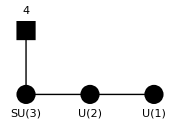

List of magnetic quivers :

---------------------

Brane Locking : {{0},{1,2,3}}

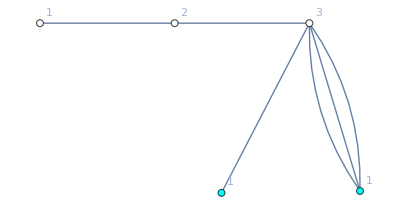
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 3
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 3 | 0 | 1 | 0) | (1
1
1
2
3)

---------------------

```mathematica
MagneticQuivers[{4,0,0},{3,2,1},{"s","u","u"},True]
```

Electric quiver :

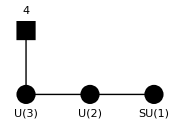

List of magnetic quivers :

---------------------

Brane Locking : {{0,1,2},{3}}

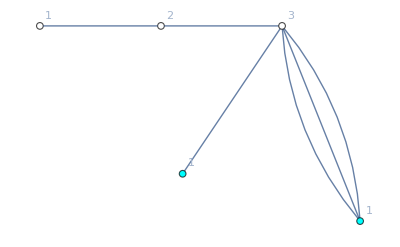
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 0 | 0 | 3
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
3 | 1 | 0 | 1 | 0) | (1
1
1
2
3)

---------------------

```mathematica
MagneticQuivers[{4,0,0},{3,2,1},{"u","u","s"},True]
```

Electric quiver :

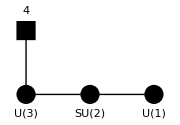

List of magnetic quivers :

---------------------

Brane Locking : {{0,1},{2,3}}

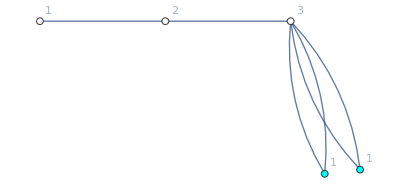
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
2 | 2 | 0 | 1 | 0) | (1
1
1
2
3)

---------------------

```mathematica
MagneticQuivers[{4,0,0},{3,2,1},{"u","s","u"},True]
```

Electric quiver :

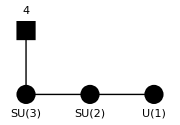

List of magnetic quivers :

---------------------

Brane Locking : {{0},{1},{2,3}}

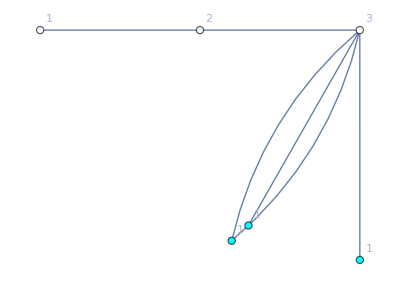
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 2 | 0 | 1 | 0) | (1
1
1
1
2
3)

---------------------

```mathematica
MagneticQuivers[{4,0,0},{3,2,1},{"s","s","u"},True]
```

Electric quiver :

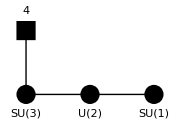

List of magnetic quivers :

---------------------

Brane Locking : {{0},{1,2},{3}}

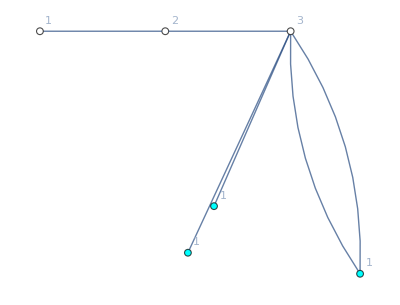
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
1 | 2 | 1 | 0 | 1 | 0) | (1
1
1
1
2
3)

---------------------

```mathematica
MagneticQuivers[{4,0,0},{3,2,1},{"s","u","s"},True]
```

Electric quiver :

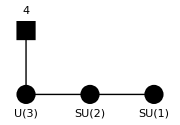

List of magnetic quivers :

---------------------

Brane Locking : {{0,1},{2},{3}}

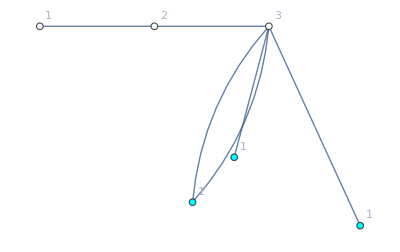
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
2 | 1 | 1 | 0 | 1 | 0) | (1
1
1
1
2
3)

---------------------

```mathematica
MagneticQuivers[{4,0,0},{3,2,1},{"u","s","s"},True]
```

Electric quiver :

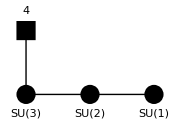

List of magnetic quivers :

---------------------

Brane Locking : {{0},{1},{2},{3}}

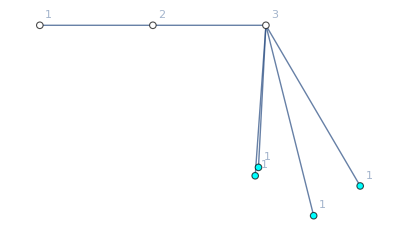
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0 | 1 | 0) | (1
1
1
1
1
2
3)

---------------------

```mathematica
MagneticQuivers[{4,0,0},{3,2,1},{"s","s","s"},True]
```

#### Main example of Section 3

Electric quiver :

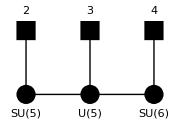

List of magnetic quivers :

---------------------

Brane Locking : {{0,1,2,3}}

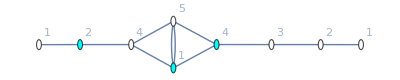
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
2 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1
1
2
4
5
4
3
2
1)

---------------------

Brane Locking : {{0},{1,2,3}}

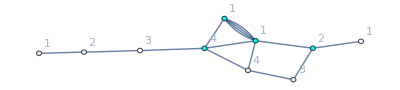
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 4 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
4 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1
1
1
2
3
4
4
3
2
1)

---------------------

Brane Locking : {{1,2},{0,3}}

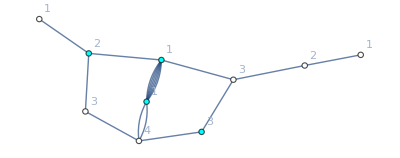
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 6 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
6 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1
1
1
2
3
4
3
3
2
1)

---------------------

Brane Locking : {{3},{0,1,2}}

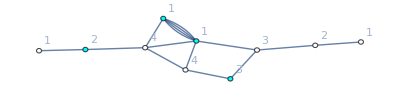
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 4 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
4 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1
1
1
2
4
4
3
3
2
1)

---------------------

Brane Locking : {{0},{1,2},{3}}

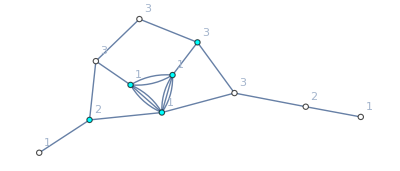
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 3 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
3 | 0 | 3 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
2 | 3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1
1
1
1
2
3
3
3
3
2
1)

---------------------

```mathematica
MagneticQuivers[{2,3,4},{5,5,6},{"s","u","s"},False]
```

#### Other examples discussed in Section 4.1

Electric quiver :

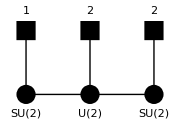

List of magnetic quivers :

---------------------

Brane Locking : {{0},{1,2},{3}}

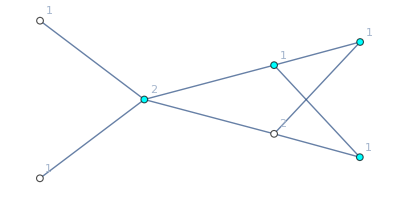
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0) | (1
1
1
1
2
2
1)

---------------------

```mathematica
MagneticQuivers[{1,2,2},{2,2,2},{"s","u","s"},False]
```

Electric quiver :

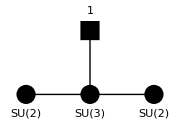

List of magnetic quivers :

---------------------

Brane Locking : {{0,2},{1,3}}

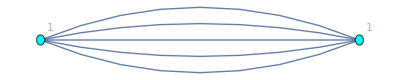
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 5
5 | 0) | (1
1)

---------------------

Brane Locking : {{1},{2},{0,3}}

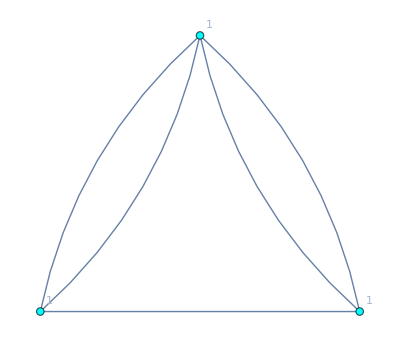
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 1 | 2
1 | 0 | 2
2 | 2 | 0) | (1
1
1)

---------------------

```mathematica
MagneticQuivers[{0,1,0},{2,3,2},{"s","s","s"},False]
```

#### Examples Summarised in Table 7

Electric quiver :

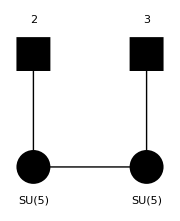

List of magnetic quivers :

---------------------

Brane Locking : {{0},{1,2}}

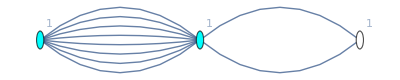
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 8 | 0
8 | 0 | 2
0 | 2 | 0) | (1
1
1)

---------------------

Brane Locking : {{1},{0,2}}

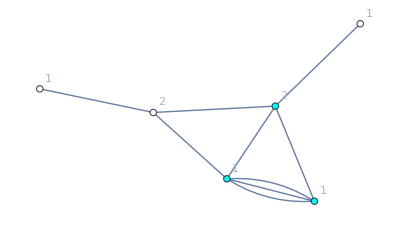
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 3 | 0 | 1 | 0 | 0
3 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0) | (1
1
1
2
2
1)

---------------------

Brane Locking : {{2},{0,1}}

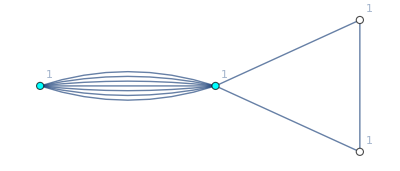
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 7 | 0 | 0
7 | 0 | 1 | 1
0 | 1 | 0 | 1
0 | 1 | 1 | 0) | (1
1
1
1)

---------------------

Brane Locking : {{0},{1},{2}}

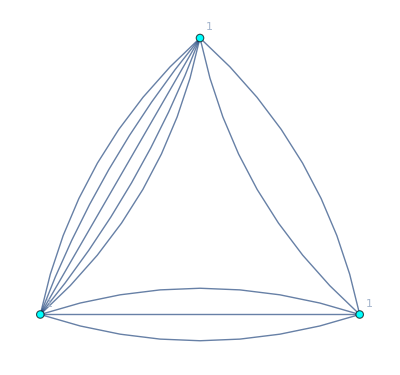
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 3 | 5
3 | 0 | 2
5 | 2 | 0) | (1
1
1)

---------------------

```mathematica
MagneticQuivers[{2,3},{5,5},{"s","s"},False]
```

Electric quiver :

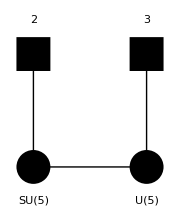

List of magnetic quivers :

---------------------

Brane Locking : {{0,1,2}}

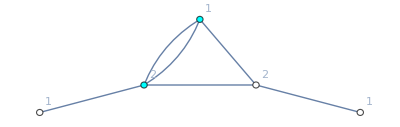
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 2 | 1 | 0
0 | 0 | 1 | 0 | 0
2 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0) | (1
1
2
2
1)

---------------------

Brane Locking : {{0},{1,2}}

Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 8 | 0
8 | 0 | 2
0 | 2 | 0) | (1
1
1)

---------------------

```mathematica
MagneticQuivers[{2,3},{5,5},{"s","u"},False]
```

Electric quiver :

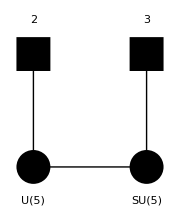

List of magnetic quivers :

---------------------

Brane Locking : {{0,1,2}}

Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 2 | 1 | 0
0 | 0 | 1 | 0 | 0
2 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0) | (1
1
2
2
1)

---------------------

Brane Locking : {{0,1},{2}}

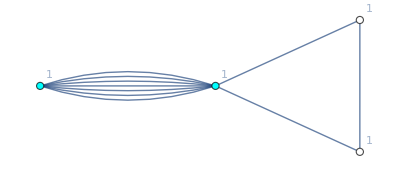
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 7 | 1 | 1
7 | 0 | 0 | 0
1 | 0 | 0 | 1
1 | 0 | 1 | 0) | (1
1
1
1)

---------------------

```mathematica
MagneticQuivers[{2,3},{5,5},{"u","s"},False]
```

Electric quiver :

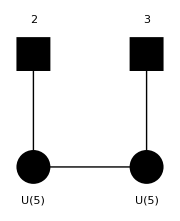

List of magnetic quivers :

---------------------

Brane Locking : {{0,1,2}}

Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 2 | 1 | 0
0 | 0 | 1 | 0 | 0
2 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0) | (1
1
2
2
1)

---------------------

```mathematica
MagneticQuivers[{2,3},{5,5},{"u","u"},False]
```

### Examples from other papers (Argyres Douglas Theories)

#### Example 5.16 in 2012.12852

Electric quiver :

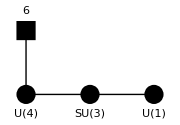

List of magnetic quivers :

---------------------

Brane Locking : {{0,1},{2,3}}

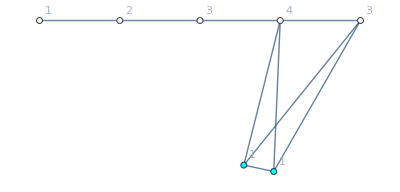
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 1 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0) | (1
1
1
2
3
4
3)

---------------------

```mathematica
MagneticQuivers[{6,0,0},{4,3,1},{"u","s","u"},True]
```

#### Example 5.22 in 2012.12852

Electric quiver :

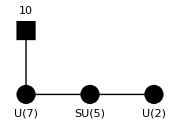

List of magnetic quivers :

---------------------

Brane Locking : {{0,1},{2,3}}

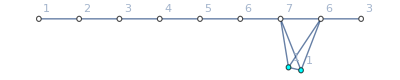
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1
1
1
2
3
4
5
6
7
6
3)

---------------------

```mathematica
MagneticQuivers[{10,0,0},{7,5,2},{"u","s","u"},True]
```

#### Example 5.24 in 2012.12852

Electric quiver :

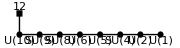

List of magnetic quivers :

---------------------

Brane Locking : {{0,1},{2},{3,4,5},{6,7,8}}

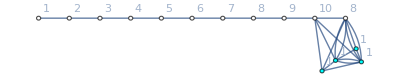
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2
1 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1
1
1
1
1
2
3
4
5
6
7
8
9
10
8)

---------------------

```mathematica
MagneticQuivers[{12,0,0,0,0,0,0,0},{10,9,8,6,5,4,2,1},{"u","s","s","u","u","s","u","u"},True]
```

#### D_ 6(SU(9)) theory from 2012.12827

Electric quiver :

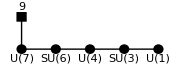

List of magnetic quivers :

---------------------

Brane Locking : {{0,1},{2,3},{4,5}}

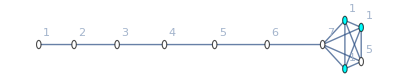
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1
1
1
1
2
3
4
5
6
7
5)

---------------------

```mathematica
MagneticQuivers[{9,0,0,0,0},{7,6,4,3,1},{"u","s","u","s","u"},False]
```

#### Example 4 in 2012.12827 (Also Section 4.4 of our paper)

Electric quiver :

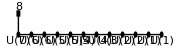

List of magnetic quivers :

---------------------

Brane Locking : {{0,1,2,3,4,5,6},{7,8,9,10,11,12}}

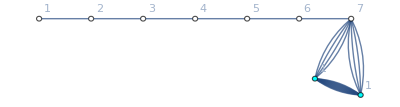
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 4
12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
4 | 4 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1
1
1
2
3
4
5
6
7)

---------------------

```mathematica
MagneticQuivers[{8,0,0,0,0,0,0,0,0,0,0,0},{7,6,6,5,5,4,4,3,2,2,1,1},{"u","u","u","u","u","u","s","u","u","u","u","u"},True]
```

Electric quiver :

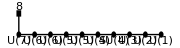

List of magnetic quivers :

---------------------

Brane Locking : {{0,1,2,3,4,5,6},{7,8,9,10}}

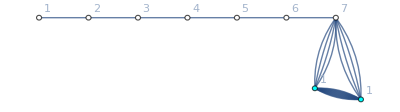
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 4
12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
4 | 4 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1
1
1
2
3
4
5
6
7)

---------------------

```mathematica
MagneticQuivers[{8,0,0,0,0,0,0,0,0,0},{7,6,6,5,5,4,4,3,2,1},{"u","u","u","u","u","u","s","u","u","u"},True]
```

Electric quiver :

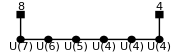

List of magnetic quivers :

---------------------

Brane Locking : {{0,1,2,3,4,5,6}}

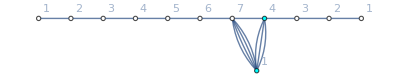
Quiver | Adjacency Matrix | Ranks U(n)
-Graphics- | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 3 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
4 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (1
1
2
3
4
5
6
7
4
3
2
1)

---------------------

```mathematica
MagneticQuivers[{8,0,0,0,0,4},{7,6,5,4,4,4},{"u","u","u","u","u","u"},True]
```